```mathematica
Get["/Users/4tc/Dropbox/suli 2018 project/zz_FINAL/BC dist sim/listed-data.txt"];
dist1Data={listedCovar1,listedCovar2,listedCorr1,listedCorr2};
Get["/Users/4tc/Dropbox/suli 2018 project/zz_FINAL/BCSC dist sim/listed-data.txt"];
dist2Data={listedCovar1,listedCovar2,listedCorr1,listedCorr2};
Get["/Users/4tc/Dropbox/suli 2018 project/zz_FINAL/BCSCNS dist sim/listed-data.txt"];
dist3Data={listedCovar1,listedCovar2,listedCorr1,listedCorr2};
Get["/Users/4tc/Dropbox/suli 2018 project/zz_FINAL/WB dist sim/listed-data.txt"];
dist4Data={listedCovar1,listedCovar2,listedCorr1,listedCorr2};
```

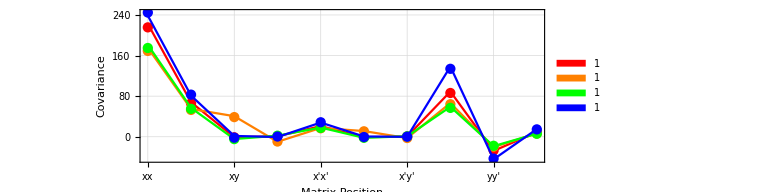

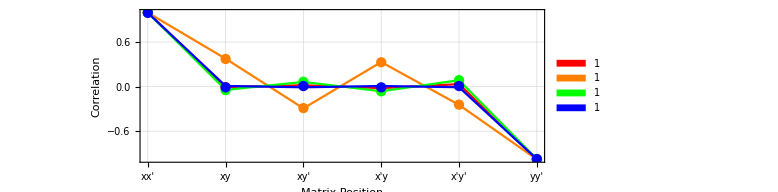

```mathematica
p1=ListPlot[
{dist1Data[[1]],dist1Data[[2]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{{True,True},{True,True}}, FrameLabel->{"Matrix Position","Covariance"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx","xx'","xy","xy'","x'x'","x'y","x'y'","yy","yy'","y'y'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Red,Red},PlotLegends->SwatchLegend[{"1"}]
];
q1=ListPlot[
{dist1Data[[3]],dist1Data[[4]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{True}, FrameLabel->{"Matrix Position","Correlation"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx'","xy","xy'","x'y","x'y'","yy'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Red,Red},PlotLegends->SwatchLegend[{"1"}]
];

p2=ListPlot[
{dist2Data[[1]],dist2Data[[2]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{{True,True},{True,True}}, FrameLabel->{"Matrix Position","Covariance"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx","xx'","xy","xy'","x'x'","x'y","x'y'","yy","yy'","y'y'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Orange,Orange},PlotLegends->SwatchLegend[{"1"}]
];
q2=ListPlot[
{dist2Data[[3]],dist2Data[[4]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{True}, FrameLabel->{"Matrix Position","Correlation"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx'","xy","xy'","x'y","x'y'","yy'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Orange,Orange},PlotLegends->SwatchLegend[{"1"}]
];

p3=ListPlot[
{dist3Data[[1]],dist3Data[[2]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{{True,True},{True,True}}, FrameLabel->{"Matrix Position","Covariance"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx","xx'","xy","xy'","x'x'","x'y","x'y'","yy","yy'","y'y'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Green,Green},PlotLegends->SwatchLegend[{"1"}]
];
q3=ListPlot[
{dist3Data[[3]],dist3Data[[4]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{True}, FrameLabel->{"Matrix Position","Correlation"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx'","xy","xy'","x'y","x'y'","yy'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Green,Green},PlotLegends->SwatchLegend[{"1"}]
];

p4=ListPlot[
{dist4Data[[1]],dist4Data[[2]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{{True,True},{True,True}}, FrameLabel->{"Matrix Position","Covariance"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx","xx'","xy","xy'","x'x'","x'y","x'y'","yy","yy'","y'y'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Blue,Blue},PlotLegends->SwatchLegend[{"1"}]
];
q4=ListPlot[
{dist4Data[[3]],dist4Data[[4]]},
Joined->{False, True}, PlotRange->All, ImageSize->Large,
Frame->{True}, FrameLabel->{"Matrix Position","Correlation"}, GridLines->Automatic,
FrameTicks->{MapIndexed[{First@#2,#1}&,{"xx'","xy","xy'","x'y","x'y'","yy'"}],Automatic},
AspectRatio->1/3,PlotStyle->{Blue,Blue},PlotLegends->SwatchLegend[{"1"}]
];

Show[p1,p2,p3,p4, PlotRange->All(*ImageSize->1200,LabelStyle->{Bold,FontSize->20},*) ]
Show[q1,q2,q3,q4, PlotRange->All(*ImageSize->1200,LabelStyle->{Bold,FontSize->20}*)]
```